## Brian — PS 10 — 2025-02-25 — Solution

## EIWL3 Sections 26, 27, and 28

## Exercises from EIWL3 Section 26

```mathematica
(* 26.1 *) Power[#,2]&/@Range[20]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
(* 26.2 *) Blend[{Red,#}]&/@{Yellow,Green,Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

```mathematica
(* 26.3 *) Framed[Column[{ToUpperCase[#],#}]]&/@Alphabet[]
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

```mathematica
(* 26.4 *)Framed[Style[#,RandomColor[]],Background->RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}






France | -Graphics-
Germany | -Graphics-
Japan | -Graphics-
United Kingdom | -Graphics-
United States | -Graphics-

```mathematica
(* 26.5 *) {EntityValue[#,"Name"],EntityValue[#,"Flag"]}&/@EntityList[EntityClass["Country","GroupOf5"]]//Grid[#,Frame->All]&
```

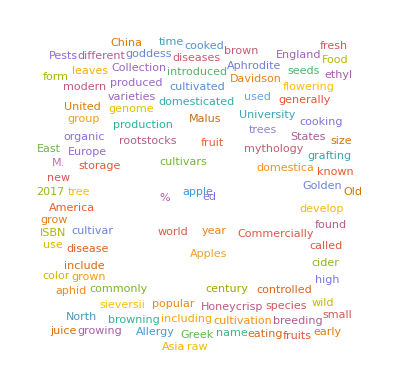
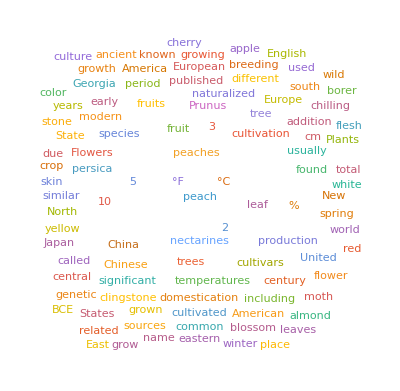
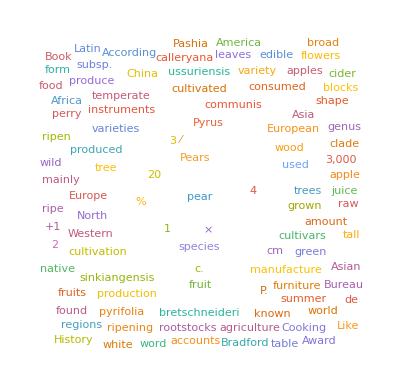

```mathematica
(* 26.6 *) WordCloud[WikipediaData[#]]&/@{"apple","peach","pear"}
```

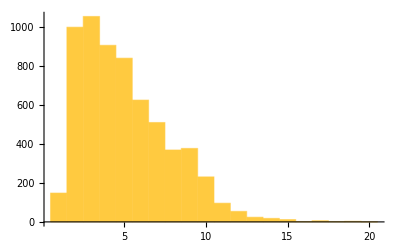
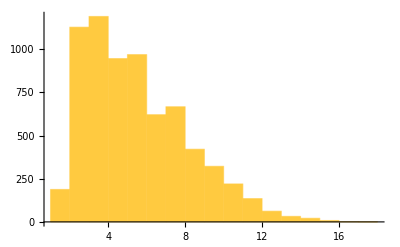
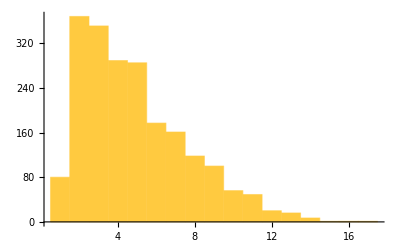

```mathematica
(* 26.7 *) Histogram[StringLength[TextWords[WikipediaData[#]]]]&/@{"apple","peach","pear"}
```

```mathematica
(* 26.8 *)GeoListPlot[#,GeoRange->EntityClass["Country","CentralAmerica"]]&/@EntityList[ EntityClass["Country","CentralAmerica"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Exercises from EIWL3 Section 27

```mathematica
(* 27.1 *) (* I really should re-read 26. *)
```

## Exercises from EIWL3 Section 28